```mathematica
D[(1+ϵ x+Sqrt[x+ϵ])/(1+Sqrt[x+ϵ Exp[-x/ϵ]]),x]
```

-((1-ⅇ^(-x/ϵ)) (1+x ϵ+√(x+ϵ)))/(2 √(x+ⅇ^(-x/ϵ) ϵ) (1+√(x+ⅇ^(-x/ϵ) ϵ))^2)+(ϵ+1/(2 √(x+ϵ)))/(1+√(x+ⅇ^(-x/ϵ) ϵ))

```mathematica
Simplify[-((1-ⅇ^(-x/ϵ)) (1+x ϵ+√(x+ϵ)))/(2 √(x+ⅇ^(-x/ϵ) ϵ) (1+√(x+ⅇ^(-x/ϵ) ϵ))^2)+(ϵ+1/(2 √(x+ϵ)))/(1+√(x+ⅇ^(-x/ϵ) ϵ))]
```

-((1-ⅇ^(-x/ϵ)) (1+x ϵ+√(x+ϵ)))/(2 √(x+ⅇ^(-x/ϵ) ϵ) (1+√(x+ⅇ^(-x/ϵ) ϵ))^2)+(2 ϵ+1/(√(x+ϵ)))/(2+2 √(x+ⅇ^(-x/ϵ) ϵ))

```mathematica
FullSimplify[-((1-ⅇ^(-x/ϵ)) (1+x ϵ+√(x+ϵ)))/(2 √(x+ⅇ^(-x/ϵ) ϵ) (1+√(x+ⅇ^(-x/ϵ) ϵ))^2)+(ϵ+1/(2 √(x+ϵ)))/(1+√(x+ⅇ^(-x/ϵ) ϵ))]
```

-((1-ⅇ^(-x/ϵ)) (1+x ϵ+√(x+ϵ)))/(2 √(x+ⅇ^(-x/ϵ) ϵ) (1+√(x+ⅇ^(-x/ϵ) ϵ))^2)+(2 ϵ+1/(√(x+ϵ)))/(2+2 √(x+ⅇ^(-x/ϵ) ϵ))

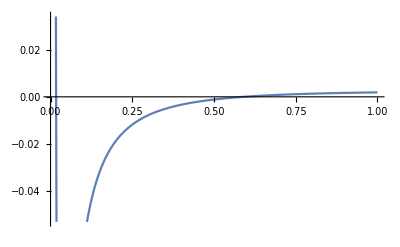

```mathematica
Plot[%,{x,0,1}]
```

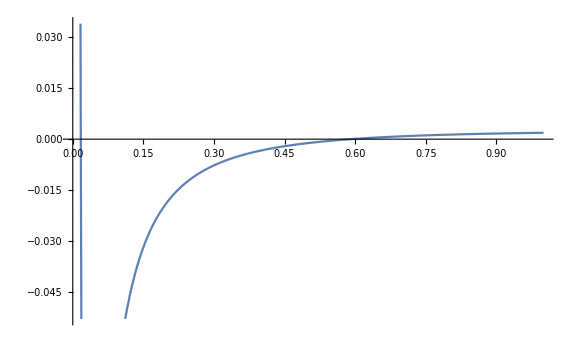

```mathematica
Show[%2,ImageSize->Large]
```

```mathematica
Clear[x]
```

```mathematica
(1+ϵ x+Sqrt[x+ϵ])/(1+Sqrt[x+ϵ Exp[-x/ϵ]])-1
```

-1+(1+x ϵ+√(x+ϵ))/(1+√(x+ⅇ^(-x/ϵ) ϵ))

```mathematica
%/ϵ^(1/2)
```

(-1+(1+x ϵ+√(x+ϵ))/(1+√(x+ⅇ^(-x/ϵ) ϵ)))/(√ϵ)

```mathematica
Limit[(-1+(1+x ϵ+√(x+ϵ))/(1+√(x+ⅇ^(-x/ϵ) ϵ)))/(√ϵ),ϵ->0]
```

Limit[(-1+(1+x ϵ+√(x+ϵ))/(1+√(x+ⅇ^(-x/ϵ) ϵ)))/(√ϵ),ϵ→0]

```mathematica
Simplify[%]
```

(-1+(1+x ϵ+√(x+ϵ))/(1+√(x+ⅇ^(-x/ϵ) ϵ)))/ϵ

```mathematica
FullSimplify[%]
```

(-1+(1+x ϵ+√(x+ϵ))/(1+√(x+ⅇ^(-x/ϵ) ϵ)))/ϵ

```mathematica
Limit[%12,ϵ->0]
```

```mathematica
x:=.5
```

```mathematica
Limit[(-1+(1+x ϵ+√(x+ϵ))/(1+√(x+ⅇ^(-x/ϵ) ϵ)))/ϵ,ϵ->0]
```

0.707107

```mathematica
x:=.5
```

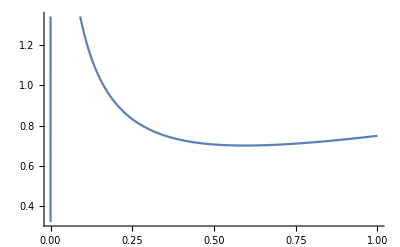

```mathematica
Plot[(-1+(1+x .001+√(x+.001))/(1+√(x+ⅇ^(-x/(.001)) .001)))/(.001),{x,0,1}]
```

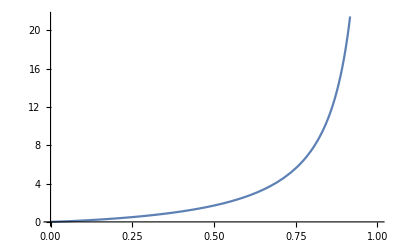

```mathematica
Plot[(x)/(1-Sqrt[x]),{x,0,1}]
```

```mathematica
Series[(1+ϵ x+Sqrt[x+ϵ])/(1+Sqrt[x+ϵ Exp[-x/ϵ]]),{ϵ,0,1}]
```

```mathematica
((1+√x)+(1/(2 √x)+x) ϵ+O[ϵ]^2)/(1+√(ⅇ^(-x/ϵ) (ⅇ^(x/ϵ) x+(ϵ+O[ϵ]^2))))

D[(1+ϵ x+Sqrt[x+ϵ])/(1+Sqrt[x+ϵ Exp[-x/ϵ]]),ϵ]
```

((1+√x)+(1/(2 √x)+x) ϵ+O[ϵ]^2)/(1+√(ⅇ^(-x/ϵ) (ⅇ^(x/ϵ) x+(ϵ+O[ϵ]^2))))

-((ⅇ^(-x/ϵ)+(ⅇ^(-x/ϵ) x)/ϵ) (1+x ϵ+√(x+ϵ)))/(2 √(x+ⅇ^(-x/ϵ) ϵ) (1+√(x+ⅇ^(-x/ϵ) ϵ))^2)+(x+1/(2 √(x+ϵ)))/(1+√(x+ⅇ^(-x/ϵ) ϵ))

```mathematica
Series[Sqrt[1+x+ϵ/(ϵ+x)],{ϵ,0,2}]
```

√(1+x)+ϵ/(2 x √(1+x))+((-5-4 x) ϵ^2)/(8 x^2 (1+x)^(3/2))+O[ϵ]^3

```mathematica
Plot[(1+Sqrt[x]+.01(1/(2Sqrt[x])+x))/(1+Sqrt[x+.01 Exp[-x/.01]]),{x,0,1}]
```

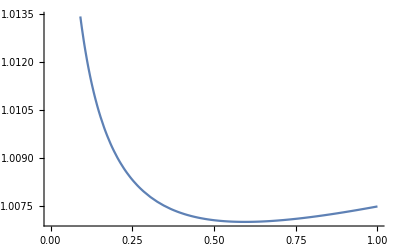
```mathematica
-Graphics-
D[Sqrt[1+x+ϵ/(ϵ+x)],ϵ]
```

-Graphics-

(-ϵ/(x+ϵ)^2+1/(x+ϵ))/(2 √(1+x+ϵ/(x+ϵ)))

```mathematica
Simplify[(-ϵ/(x+ϵ)^2+1/(x+ϵ))/(2 √(1+x+ϵ/(x+ϵ)))]
```

x/(2 (x+ϵ)^2 √(1+x+ϵ/(x+ϵ)))

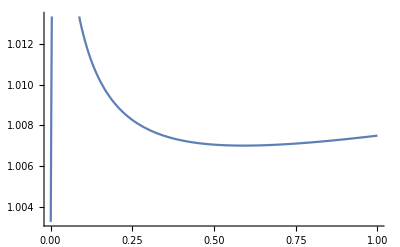

```mathematica
Plot[(1+.01 x+Sqrt[x+.01])/(1+Sqrt[x+.01Exp[-x/.01]]),{x,0,1}]
```

```mathematica
Simplify[%12]
```

((1+√x)+(1/(2 √x)+x) ϵ+O[ϵ]^2)/(1+√(x+ⅇ^(-x/ϵ) (ϵ+O[ϵ]^2)))

```mathematica
FullSimplify[%12]
```

((1+√x)+(1/(2 √x)+x) ϵ+O[ϵ]^2)/(1+√(x+ⅇ^(-x/ϵ) (ϵ+O[ϵ]^2)))

```mathematica
D[(1+ϵ x+Sqrt[x+ϵ])/(1+Sqrt[x+ϵ Exp[-x/ϵ]]),ϵ]
```

-((ⅇ^(-x/ϵ)+(ⅇ^(-x/ϵ) x)/ϵ) (1+x ϵ+√(x+ϵ)))/(2 √(x+ⅇ^(-x/ϵ) ϵ) (1+√(x+ⅇ^(-x/ϵ) ϵ))^2)+(x+1/(2 √(x+ϵ)))/(1+√(x+ⅇ^(-x/ϵ) ϵ))

```mathematica
Simplify[-((ⅇ^(-x/ϵ)+(ⅇ^(-x/ϵ) x)/ϵ) (1+x ϵ+√(x+ϵ)))/(2 √(x+ⅇ^(-x/ϵ) ϵ) (1+√(x+ⅇ^(-x/ϵ) ϵ))^2)+(x+1/(2 √(x+ϵ)))/(1+√(x+ⅇ^(-x/ϵ) ϵ))]
```

-(ⅇ^(-x/ϵ) (x+ϵ) (1+x ϵ+√(x+ϵ)))/(2 ϵ √(x+ⅇ^(-x/ϵ) ϵ) (1+√(x+ⅇ^(-x/ϵ) ϵ))^2)+(2 x+1/(√(x+ϵ)))/(2+2 √(x+ⅇ^(-x/ϵ) ϵ))

```mathematica
Limit[%,ϵ->0]
```

Limit[-(ⅇ^(-x/ϵ) (x+ϵ) (1+x ϵ+√(x+ϵ)))/(2 ϵ √(x+ⅇ^(-x/ϵ) ϵ) (1+√(x+ⅇ^(-x/ϵ) ϵ))^2)+(2 x+1/(√(x+ϵ)))/(2+2 √(x+ⅇ^(-x/ϵ) ϵ)),ϵ→0]

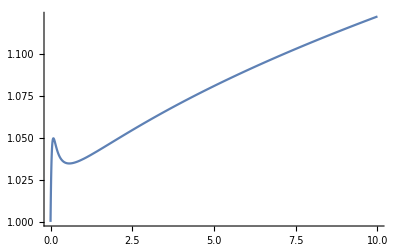

```mathematica
Plot[(1+.05 x+Sqrt[x+.05])/(1+Sqrt[x+.05 Exp[-x/.05]]),{x,0,10}]
```